```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jenna/jennaproject/mma

```mathematica
Needs["Integrals`"]
```

Needs::nocont: Context Integrals` was not created when Needs was evaluated.

```mathematica
mp0=Import["../data/test_matterPower_0.dat","Table"];
trlist=Import["../data/Tru_Tm.txt","Table"];
```

```mathematica
Pm=Interpolation[mp0];
tr=Interpolation[trlist];
```

```mathematica
Pmgood[k_]:=If[k<0.0001||k>1.993,0,Pm[k]];
Trgood[k_]:=If[k<1.9755223192*^-7||k>12.477498542,0,tr[k]];
```

```mathematica
kvals=Union[Range[0.001,0.4,0.001],Range[0.4,1,0.03]];
Dimensions[kvals]
```

{420}

```mathematica
t1=#^3/(2*Pi^2)*term1[#,Pmgood]&/@kvals;
t2=#^3/(2*Pi^2)*term2[#,Pmgood]&/@kvals;
t3=#^3/(2*Pi^2)*term3[#,Pmgood,Trgood]&/@kvals;
t4=#^3/(2*Pi^2)*term4[#,Pmgood,Trgood]&/@kvals;
t5=#^3/(2*Pi^2)*term5[#,Pmgood,Trgood]&/@kvals;
```

Suave::success: Needed 40000 function evaluations on 40 subregions.

Suave::success: Needed 29000 function evaluations on 29 subregions.

Suave::success: Needed 15000 function evaluations on 15 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 50000 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 50000 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 19000 function evaluations on 19 subregions.

Suave::success: Needed 15000 function evaluations on 15 subregions.

Suave::success: Needed 16000 function evaluations on 16 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 29000 function evaluations on 29 subregions.

Suave::success: Needed 21000 function evaluations on 21 subregions.

Suave::success: Needed 17000 function evaluations on 17 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

```mathematica
Export["~/jennaproject/data/kvals.txt",kvals];
Export["~/jennaproject/data/b2b2.txt",t1];
Export["~/jennaproject/data/b1b2.txt",t2];
Export["~/jennaproject/data/b1br.txt",t3];
Export["~/jennaproject/data/b2br.txt",t4];
Export["~/jennaproject/data/brbr.txt",t5];
```

```mathematica
Dimensions[t1]
Dimensions[t2]
Dimensions[t3]
Dimensions[t4]
Dimensions[t5]
Dimensions[kvals]
```

{420}

{420}

{420}

«3 more identical outputs»

```mathematica
Plin=Pmgood[#]&/@kvals;
```

```mathematica
Export["~/jennaproject/data/plin.txt",Plin];
```

```mathematica
kvals;
```

```mathematica
h=0.703
```

0.703

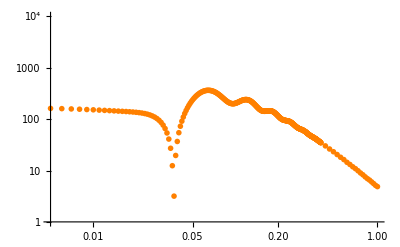

```mathematica
γ3=ListLogLogPlot[Thread[{kvals,Abs[t3+t4]/h^3}],PlotRange->{{0.005,1},{1,10^4}},PlotMarkers-> {mark3, .02}]
```